```mathematica
ol300c24h=metabgensteadystate[24,0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{2890.3,Null}

```mathematica
{hp300ckill1,hp300ckill10,hp300ckill50,hp300ckill90,hp300ckill99,hpkill3000,hpkill6000}=Parallelize[{mxcontkilling[24,ol300c24h[[1]],1,2.1,163,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],1,2.1,233,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],1,2.1,337,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],1,2.1,472,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],1,2.1,608,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],1,2.1,3000,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],1,2.1,6000,1,0,0,0,0,0,0,14,0.02]}];//AbsoluteTiming
```

{3711.93,Null}

```mathematica
{hyp300ckill1,hyp300ckill10,hyp300ckill50,hyp300ckill90,hyp300ckill99}=Parallelize[{mxcontkilling[24,ol300c24h[[1]],0,2.1,0,0,2,1,0,0,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],0,2.1,0,0,4,1,0,0,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],0,2.1,0,0,7,1,0,0,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],0,2.1,0,0,10,1,0,0,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],0,2.1,0,0,14,1,0,0,0,0,14,0.02]}];//AbsoluteTiming
```

{1131.03,Null}

```mathematica
{hmu300ckill1,hmu300ckill10,hmu300ckill50,hmu300ckill90,hmu300ckill99,hmu300ckill7000,hmu300ckill14000}=Parallelize[{mxcontkilling[24,ol300c24h[[1]],2,2.1,0,0,0,0,563,1,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],2,2.1,0,0,0,0,663,1,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],2,2.1,0,0,0,0,767,1,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],2,2.1,0,0,0,0,880,1,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],2,2.1,0,0,0,0,1030,1,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],2,2.1,0,0,0,0,7000,1,0,0,14,0.02],mxcontkilling[24,ol300c24h[[1]],2,2.1,0,0,0,0,14000,1,0,0,14,0.02]}];//AbsoluteTiming
```

{3772.53,Null}

```mathematica
{hmp300cgen1,hmp300cgen10,hmp300cgen50,hmp300cgen90,hmp300cgen99}=Parallelize[{metabgensteadystate[24,0,2.1,0,0,0,0,0,0,563,1,14,0.02],metabgensteadystate[24,0,2.1,0,0,0,0,0,0,663,1,14,0.02],metabgensteadystate[24,0,2.1,0,0,0,0,0,0,767,1,14,0.02],metabgensteadystate[24,0,2.1,0,0,0,0,0,0,880,1,14,0.02],metabgensteadystate[24,0,2.1,0,0,0,0,0,0,1030,1,14,0.02]}];//AbsoluteTiming
```

{4137.44,Null}

```mathematica
Export["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\HMP300CGEN.mx",{hmp300cgen1,hmp300cgen10,hmp300cgen50,hmp300cgen90,hmp300cgen99}];
```

```mathematica
{hmp300cgen1,hmp300cgen10,hmp300cgen50,hmp300cgen90,hmp300cgen99}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\HMP300CGEN.mx"];
```

```mathematica
{hmp300ckill1,hmp300ckill10,hmp300ckill50,hmp300ckill90,hmp300ckill99}=Parallelize[{mxcontkilling[24,ol300c24h[[1]],0,2.1,0,0,0,0,0,0,563,1,14,0.02],mxcontkilling[24,ol300c24h[[1]],0,2.1,0,0,0,0,0,0,663,1,14,0.02],mxcontkilling[24,ol300c24h[[1]],0,2.1,0,0,0,0,0,0,767,1,14,0.02],mxcontkilling[24,ol300c24h[[1]],0,2.1,0,0,0,0,0,0,880,1,14,0.02],mxcontkilling[24,ol300c24h[[1]],0,2.1,0,0,0,0,0,0,1030,1,14,0.02]}];//AbsoluteTiming
```

{1931.67,Null}

```mathematica
{hmp300ckill1,hmp300ckill10,hmp300ckill50,hmp300ckill90,hmp300ckill99}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarhmp300c.mx"];
```

```mathematica
Export["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarhmp300c.mx",{hmp300ckill1,hmp300ckill10,hmp300ckill50,hmp300ckill90,hmp300ckill99}];
```

```mathematica
{hmp400ckill1,hmp400ckill10,hmp400ckill50,hmp400ckill90,hmp400ckill99}=Parallelize[{mxcontkilling[24,ol400c24h[[1]],0,2.1,0,0,0,0,0,0,563,1,14,0.02],mxcontkilling[24,ol400c24h[[1]],0,2.1,0,0,0,0,0,0,663,1,14,0.02],mxcontkilling[24,ol400c24h[[1]],0,2.1,0,0,0,0,0,0,767,1,14,0.02],mxcontkilling[24,ol400c24h[[1]],0,2.1,0,0,0,0,0,0,880,1,14,0.02],mxcontkilling[24,ol400c24h[[1]],0,2.1,0,0,0,0,0,0,1030,1,14,0.02]}];//AbsoluteTiming
```

{1765.19,Null}

```mathematica
Export["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarhmp400c.mx",{hmp400ckill1,hmp400ckill10,hmp400ckill50,hmp400ckill90,hmp400ckill99}];
```

```mathematica
{hmp400ckill1,hmp400ckill10,hmp400ckill50,hmp400ckill90,hmp400ckill99}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarhmp400c.mx"];
```

```mathematica
ol400c24h=metabgensteadystate[24,0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{2791.13,Null}

```mathematica
Export["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarol400c.mx",{ol400c24h}];
```

```mathematica
{hp400ckill1,hp400ckill10,hp400ckill50,hp400ckill90,hp400ckill99,hpkill3000,hpkill6000}=Parallelize[{mxcontkilling[24,ol400c24h[[1]],1,2.1,163,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],1,2.1,233,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],1,2.1,337,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],1,2.1,472,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],1,2.1,608,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],1,2.1,3000,1,0,0,0,0,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],1,2.1,6000,1,0,0,0,0,0,0,14,0.02]}];//AbsoluteTiming
```

{5255.41,Null}

```mathematica
Export["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarhp400c.mx",{hp400ckill1,hp400ckill10,hp400ckill50,hp400ckill90,hp400ckill99,hpkill3000,hpkill6000}];
```

```mathematica
{hyp400ckill1,hyp400ckill10,hyp400ckill50,hyp400ckill90,hyp400ckill99}=Parallelize[{mxcontkilling[24,ol400c24h[[1]],0,2.1,0,0,2,1,0,0,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],0,2.1,0,0,4,1,0,0,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],0,2.1,0,0,7,1,0,0,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],0,2.1,0,0,10,1,0,0,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],0,2.1,0,0,14,1,0,0,0,0,14,0.02]}];//AbsoluteTiming
```

{1526.65,Null}

```mathematica
Export["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarhyp400c.mx",{hyp400ckill1,hyp400ckill10,hyp400ckill50,hyp400ckill90,hyp400ckill99}];
```

```mathematica
{hmu400ckill1,hmu400ckill10,hmu400ckill50,hmu400ckill90,hmu400ckill99,hmu400ckill7000,hmu400ckill14000}=Parallelize[{mxcontkilling[24,ol400c24h[[1]],2,2.1,0,0,0,0,563,1,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],2,2.1,0,0,0,0,663,1,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],2,2.1,0,0,0,0,767,1,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],2,2.1,0,0,0,0,880,1,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],2,2.1,0,0,0,0,1030,1,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],2,2.1,0,0,0,0,7000,1,0,0,14,0.02],mxcontkilling[24,ol400c24h[[1]],2,2.1,0,0,0,0,14000,1,0,0,14,0.02]}];//AbsoluteTiming
```

{4957.11,Null}

```mathematica
Export["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarhmu400c.mx",{hmu400ckill1,hmu400ckill10,hmu400ckill50,hmu400ckill90,hmu400ckill99,hmu400ckill7000,hmu400ckill14000}];
```

```mathematica
{hmp400cgen1,hmp400cgen10,hmp400cgen50,hmp400cgen90,hmp400cgen99}=Parallelize[{metabgensteadystate[24,0,2.1,0,0,0,0,0,0,563,1,14,0.02],metabgensteadystate[24,0,2.1,0,0,0,0,0,0,663,1,14,0.02],metabgensteadystate[24,0,2.1,0,0,0,0,0,0,767,1,14,0.02],metabgensteadystate[24,0,2.1,0,0,0,0,0,0,880,1,14,0.02],metabgensteadystate[24,0,2.1,0,0,0,0,0,0,1030,1,14,0.02]}];//AbsoluteTiming
```

{5806.7,Null}

```mathematica
Export["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\HMP400cGEN.mx",{hmp400cgen1,hmp400cgen10,hmp400cgen50,hmp400cgen90,hmp400cgen99}];
```

```mathematica
{hmp400ckill1,hmp400ckill10,hmp400ckill50,hmp400ckill90,hmp400ckill99}=Parallelize[{mxcontkilling[hmp400cgen1[[1]],0,2.1,0,0,0,0,0,0,563,1,14,0.02],mxcontkilling[hmp400cgen10[[1]],0,2.1,0,0,0,0,0,0,663,1,14,0.02],mxcontkilling[hmp400cgen50[[1]],0,2.1,0,0,0,0,0,0,767,1,14,0.02],mxcontkilling[hmp400cgen90[[1]],0,2.1,0,0,0,0,0,0,880,1,14,0.02],mxcontkilling[hmp400cgen99[[1]],0,2.1,0,0,0,0,0,0,1030,1,14,0.02]}];//AbsoluteTiming
```

{0.150948,Null}

```mathematica
{hp300ckill1,hp300ckill10,hp300ckill50,hp300ckill90,hp300ckill99,hpkill3000,hpkill6000}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarhp300c.mx"];
```

```mathematica
{hp300ctyp1,hp300ctyp10,hp300ctyp50,hp300ctyp90,hp300ctyp99,hp300ctyp3000,hyp300ctyp6000}=Parallelize[{titeryieldproductivity[hp300ckill1],titeryieldproductivity[hp300ckill10],titeryieldproductivity[hp300ckill50],titeryieldproductivity[hp300ckill90],titeryieldproductivity[hp300ckill99],titeryieldproductivity[hpkill3000],titeryieldproductivity[hpkill6000]}]
```

```mathematica
{ol300c24h}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarOL300c.mx"];
```

```mathematica
{ol400c24h}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarol400c.mx"];
```

```mathematica
ol300ckill=mxcontkilling[24,ol300c24h[[1]],0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{606.947,Null}

```mathematica
ol300ctyp=titeryieldproductivity[ol300ckill];
```

```mathematica
ol400ckill=mxcontkilling[24,ol400c24h[[1]],0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{1056.17,Null}

```mathematica
ol400ctyp=titeryieldproductivity[ol400ckill];
```

```mathematica
{hp400ckill1,hp400ckill10,hp400ckill50,hp400ckill90,hp400ckill99,hp400ckill3000,hp400ckill6000}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarhp400c.mx"];
```

```mathematica
{hp400ctyp1,hp400ctyp10,hp400ctyp50,hp400ctyp90,hp400ctyp99,hp400ctyp3000,hyp400ctyp6000}=Parallelize[{titeryieldproductivity[hp400ckill1],titeryieldproductivity[hp400ckill10],titeryieldproductivity[hp400ckill50],titeryieldproductivity[hp400ckill90],titeryieldproductivity[hp400ckill99],titeryieldproductivity[hp400ckill3000],titeryieldproductivity[hp400ckill6000]}];//AbsoluteTiming
```

{5.80176,Null}

```mathematica
{ol500c24h,ol500c24hkeep,ol500c24hkill,ol500c24hmem,oltyp}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\ol500c24htest.mx"];
```

```mathematica
{hpgen1,hpgen10,hpgen50,hpgen90,hpgen99,hpkeep1,hpkeep10,hpkeep50,hpkeep90,hpkeep99,hpmem1,hpmem10,hpmem50,hpmem90,hpmem99,hpkill1,hpkill10,hpkill50,hpkill90,hpkill99,hptyp1,hptyp10,hptyp50,hptyp90,hptyp99}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\hp500c24hpercent.mx"];
```

```mathematica
{hp500ckill3000,hp500ckill6000,hptyp3000,hptyp6000}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\hplargecorrect.mx"];
```

```mathematica
hpproteintyp300={ol300ctyp[[2]]/ol300ctyp[[2]],hp300ctyp1[[2]]/ol300ctyp[[2]],hp300ctyp10[[2]]/ol300ctyp[[2]],hp300ctyp50[[2]]/ol300ctyp[[2]],hp300ctyp90[[2]]/ol300ctyp[[2]],hp300ctyp99[[2]]/ol300ctyp[[2]],hp300ctyp3000[[2]]/ol300ctyp[[2]],hyp300ctyp6000[[2]]/ol300ctyp[[2]]};
```

```mathematica
hpproteintyp400={ol400ctyp[[2]]/ol400ctyp[[2]],hp400ctyp1[[2]]/ol400ctyp[[2]],hp400ctyp10[[2]]/ol400ctyp[[2]],hp400ctyp50[[2]]/ol400ctyp[[2]],hp400ctyp90[[2]]/ol400ctyp[[2]],hp400ctyp99[[2]]/ol400ctyp[[2]],hp400ctyp3000[[2]]/ol400ctyp[[2]],hyp400ctyp6000[[2]]/ol400ctyp[[2]]};
```

```mathematica
hpproteintyp500={oltyp[[2]]/oltyp[[2]],hptyp1[[2]]/oltyp[[2]],hptyp10[[2]]/oltyp[[2]],hptyp50[[2]]/oltyp[[2]],hptyp90[[2]]/oltyp[[2]],hptyp99[[2]]/oltyp[[2]],hptyp3000[[2]]/oltyp[[2]],hptyp6000[[2]]/oltyp[[2]]}
```

{1.,1.22623,1.31077,1.40793,1.52273,1.61678,2.62064,1.68294}

```mathematica
hpproteinMean=Mean[{hpproteintyp300,hpproteintyp400,hpproteintyp500}]
```

{1.,1.24,1.32336,1.41943,1.52804,1.6246,2.64046,1.72813}

```mathematica
hpproteinerror=StandardDeviation[{hpproteintyp300,hpproteintyp400,hpproteintyp500}]
```

{0.,0.0122312,0.0195503,0.0237106,0.0221707,0.015112,0.0390134,0.107695}

```mathematica
data={hpproteintyp300,hpproteintyp400,hpproteintyp500};
```

```mathematica
Length [data]
```

3

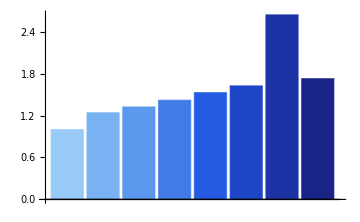
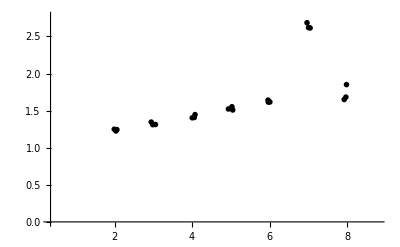
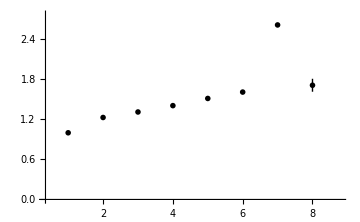

```mathematica
Overlay[{BarChart[{hpproteinMean},ChartStyle->{RGBColor["#97caf7"],RGBColor["#79b2f3"],RGBColor["#5c98ee"],
RGBColor["#407be8"],
RGBColor["#245be1"],
RGBColor["#1e45c5"],
RGBColor["#1c33a5"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium],dots,ListPlot[{Around[1,0],Around[1.22935,0.007],Around[1.31196,0.0119],Around[1.40721,0.0168],Around[1.51491,0.0179706],Around[1.61065,0.0098198],Around[2.61773,0.0264527],Around[1.71296,0.0971365]},PlotStyle->{Thick,Black},PlotRange->{{0.35,8.78},{0,2.77}},ImageSize->Medium,AxesStyle->Directive[Transparent, 16],PlotMarkers->{"", Tiny}]}]
```

```mathematica
xpos=Range[6];

rawPoints=Flatten[Table[Transpose[{ConstantArray[xpos[[i]],Length[data]],data[[All,i]]}],{i,{2,3,4,5,6,7,8}}],1];
```

Part::partw: Part 7 of {1,2,3,4,5,6} does not exist.

Part::partw: Part 8 of {1,2,3,4,5,6} does not exist.

```mathematica
jittered={#1+RandomReal[{-0.08,0.08}],#2}&@@@rawPoints;

dots=ListPlot[jittered,PlotStyle->Black,PlotMarkers->{"OpenMarkers",5},AxesStyle->Directive[Transparent, 16],PlotRange->{{0.35,8.78},{0,2.77}}];
```

```mathematica
hpmetabolitetyp300={ol300ctyp[[4]]/ol300ctyp[[4]],hp300ctyp1[[4]]/ol300ctyp[[4]],hp300ctyp10[[4]]/ol300ctyp[[4]],hp300ctyp50[[4]]/ol300ctyp[[4]],hp300ctyp90[[4]]/ol300ctyp[[4]],hp300ctyp99[[4]]/ol300ctyp[[4]],hp300ctyp3000[[4]]/ol300ctyp[[4]],hyp300ctyp6000[[4]]/ol300ctyp[[4]]};
```

```mathematica
hpmetabolitetyp400={ol400ctyp[[4]]/ol400ctyp[[4]],hp400ctyp1[[4]]/ol400ctyp[[4]],hp400ctyp10[[4]]/ol400ctyp[[4]],hp400ctyp50[[4]]/ol400ctyp[[4]],hp400ctyp90[[4]]/ol400ctyp[[4]],hp400ctyp99[[4]]/ol400ctyp[[4]],hp400ctyp3000[[4]]/ol400ctyp[[4]],hyp400ctyp6000[[4]]/ol400ctyp[[4]]};
```

```mathematica
hpmetabolitetyp500={oltyp[[4]]/oltyp[[4]],hptyp1[[4]]/oltyp[[4]],hptyp10[[4]]/oltyp[[4]],hptyp50[[4]]/oltyp[[4]],hptyp90[[4]]/oltyp[[4]],hptyp99[[4]]/oltyp[[4]],hptyp3000[[4]]/oltyp[[4]],hptyp6000[[4]]/oltyp[[4]]}
```

{1.,1.33759,1.443,1.61241,1.77394,1.91878,3.5053,2.38139}

```mathematica
hpmetaboliteMean=Mean[{hpmetabolitetyp300,hpmetabolitetyp400,hpmetabolitetyp500}]
```

{1.,1.35589,1.46721,1.61697,1.78868,1.92544,3.48371,2.1824}

```mathematica
hpmetaberror=StandardDeviation[{hpmetabolitetyp300,hpmetabolitetyp400,hpmetabolitetyp500}]
```

{0.,0.0176274,0.0345794,0.0279426,0.041816,0.0331711,0.0632789,0.212891}

```mathematica
data2={hpmetabolitetyp300,hpmetabolitetyp400,hpmetabolitetyp500};
```

```mathematica
rawPoints2=Flatten[Table[Transpose[{ConstantArray[xpos[[i]],Length[data2]],data2[[All,i]]}],{i,{2,3,4,5,6,7,8}}],1];
```

```mathematica
jittered2={#1+RandomReal[{-0.08,0.08}],#2}&@@@rawPoints2;

dots2=ListPlot[jittered2,PlotStyle->Black,PlotMarkers->{"OpenMarkers",5},AxesStyle->Directive[Transparent, 16],PlotRange->{{0.35,8.78},{0,3.59}}];
```

{{1.92321,1.37275},{2.03311,1.35732},{1.97335,1.33759},{2.97351,1.50682},{3.06622,1.45183},{2.9724,1.443},{3.97148,1.64692},{3.92773,1.59159},{3.93587,1.61241},{4.93257,1.83587},{5.00981,1.75623},{5.06519,1.77394},{5.97423,1.96144},{5.97948,1.89611},{6.05757,1.91878},{6.9356,3.53337},{6.93977,3.41247},{7.06731,3.5053},{7.98639,2.2079},{7.99015,1.9579},{8.07732,2.38139}}

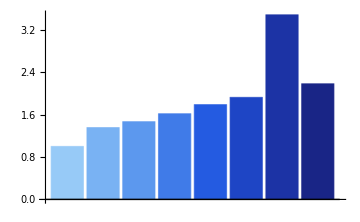
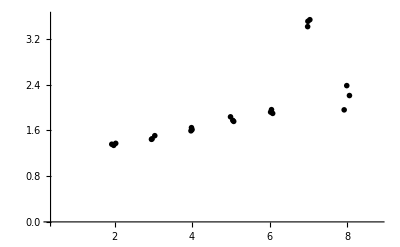
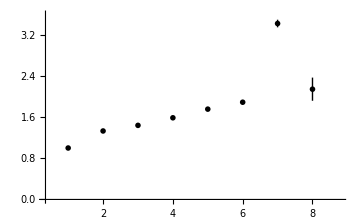

```mathematica
Overlay[{BarChart[{hpmetaboliteMean},ChartStyle->{RGBColor["#97caf7"],RGBColor["#79b2f3"],RGBColor["#5c98ee"],
RGBColor["#407be8"],
RGBColor["#245be1"],
RGBColor["#1e45c5"],
RGBColor["#1c33a5"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium],dots2,ListPlot[{Around[1,0],Around[1.33112,0.0135956],Around[1.44019,0.00573259],Around[1.58741,0.0218991],Around[1.7558,0.0201132],Around[1.89023,0.0249875],Around[3.4203,0.0740705],Around[2.1435,0.225318]},PlotStyle->{Thick,Black},PlotRange->{{0.35,8.78},{0,3.59}},ImageSize->Medium,AxesStyle->Directive[Transparent, 16],PlotMarkers->{"", Tiny}]}]
```

```mathematica
{hmu300ckill1,hmu300ckill10,hmu300ckill50,hmu300ckill90,hmu300ckill99,hmu300ckill7000,hmu300ckill14000}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarhmu300c.mx"];
```

```mathematica
{hmu300ctyp1,hmu300ctyp10,hmu300ctyp50,hmu300ctyp90,hmu300ctyp99,hmu300ctyp7000,hmu300ctyp14000}=Parallelize[{titeryieldproductivity[hmu300ckill1],titeryieldproductivity[hmu300ckill10],titeryieldproductivity[hmu300ckill50],titeryieldproductivity[hmu300ckill90],titeryieldproductivity[hmu300ckill99],titeryieldproductivity[hmu300ckill7000],titeryieldproductivity[hmu300ckill14000]}];
```

```mathematica
{hmu400ckill1,hmu400ckill10,hmu400ckill50,hmu400ckill90,hmu400ckill99,hmu400ckill7000,hmu400ckill14000}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarhmu400c.mx"];
```

```mathematica
{hmu400ctyp1,hmu400ctyp10,hmu400ctyp50,hmu400ctyp90,hmu400ctyp99,hmu400ctyp7000,hmu400ctyp14000}=Parallelize[{titeryieldproductivity[hmu400ckill1],titeryieldproductivity[hmu400ckill10],titeryieldproductivity[hmu400ckill50],titeryieldproductivity[hmu400ckill90],titeryieldproductivity[hmu400ckill99],titeryieldproductivity[hmu400ckill7000],titeryieldproductivity[hmu400ckill14000]}];
```

```mathematica
{hmugen1,hmugen10,hmugen50,hmugen90,hmugen99,hmukeep1,hmukeep10,hmukeep50,hmukeep90,hmukeep99,hmumem1,hmumem10,hmumem50,hmumem90,hmumem99,hmukill1,hmukill10,hmukill50,hmukill90,hmukill99,hmutyp1,hmutyp10,hmutyp50,hmutyp90,hmutyp99}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\hmu500c24hpercent.mx"];
```

```mathematica
{hpgen3000,hpgen6000,hmugen7000,hmugen14000,hpkeep3000,hpkeep6000,hmukeep7000,hmukeep14000,hp500kill3000,hp500kill6000,hmu500ckill7000,hmu500ckill14000}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\hphmularge.mx"];
```

```mathematica
hmutyp7000=titeryieldproductivity[hmu500ckill7000];
```

```mathematica
hmutyp14000=titeryieldproductivity[hmu500ckill14000];
```

```mathematica
hmuproteintyp300={ol300ctyp[[2]]/ol300ctyp[[2]],hmu300ctyp1[[2]]/ol300ctyp[[2]],hmu300ctyp10[[2]]/ol300ctyp[[2]],hmu300ctyp50[[2]]/ol300ctyp[[2]],hmu300ctyp90[[2]]/ol300ctyp[[2]],hmu300ctyp99[[2]]/ol300ctyp[[2]],hmu300ctyp7000[[2]]/ol300ctyp[[2]],hmu300ctyp14000[[2]]/ol300ctyp[[2]]};
```

```mathematica
hmuproteintyp400={ol400ctyp[[2]]/ol400ctyp[[2]],hmu400ctyp1[[2]]/ol400ctyp[[2]],hmu400ctyp10[[2]]/ol400ctyp[[2]],hmu400ctyp50[[2]]/ol400ctyp[[2]],hmu400ctyp90[[2]]/ol400ctyp[[2]],hmu400ctyp99[[2]]/ol400ctyp[[2]],hmu400ctyp7000[[2]]/ol400ctyp[[2]],hmu400ctyp14000[[2]]/ol400ctyp[[2]]};
```

```mathematica
hmuproteintyp500={oltyp[[2]]/oltyp[[2]],hmutyp1[[2]]/oltyp[[2]],hmutyp10[[2]]/oltyp[[2]],hmutyp50[[2]]/oltyp[[2]],hmutyp90[[2]]/oltyp[[2]],hmutyp99[[2]]/oltyp[[2]],hmutyp7000[[2]]/oltyp[[2]],hmutyp14000[[2]]/oltyp[[2]]};
```

```mathematica
hmuproteinMean=Mean[{hmuproteintyp300,hmuproteintyp400,hmuproteintyp500}]
```

{1.,1.386,1.45514,1.50514,1.56415,1.64684,1.37095,0.48538}

```mathematica
hmuproteinerror=StandardDeviation[{hmuproteintyp300,hmuproteintyp400,hmuproteintyp500}]
```

{0.,0.0153511,0.0321271,0.0419789,0.0421239,0.0231729,0.0828152,0.0133597}

```mathematica
data3={hmuproteintyp300,hmuproteintyp400,hmuproteintyp500};
```

```mathematica
rawPoints3=Flatten[Table[Transpose[{ConstantArray[xpos[[i]],Length[data3]],data3[[All,i]]}],{i,{2,3,4,5,6,7,8}}],1];
```

```mathematica
jittered3={#1+RandomReal[{-0.08,0.08}],#2}&@@@rawPoints3;

dots3=ListPlot[jittered3,PlotStyle->Black,PlotMarkers->{"OpenMarkers",5},AxesStyle->Directive[Transparent, 16],PlotRange->{{0.35,8.78},{0,1.72}}];
```

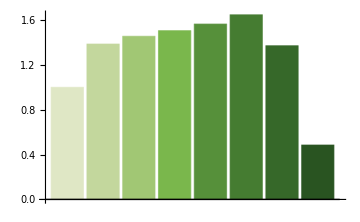
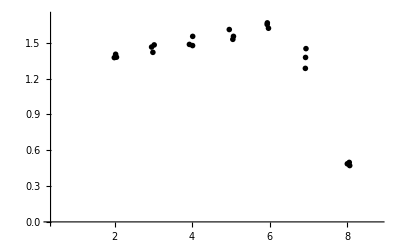
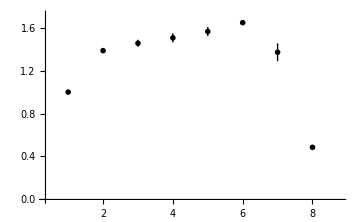

```mathematica
Overlay[{BarChart[{hmuproteinMean},ChartStyle->{RGBColor["#dfe7c5"],

RGBColor["#c3d79d"],

RGBColor["#a1c774"],

RGBColor["#7ab74c"],

RGBColor["#56903a"],
RGBColor["#457c31"],
RGBColor["#366829"],
RGBColor["#295421"]},AxesStyle->Directive[Black, 16],ImageSize->Medium],dots3,ListPlot[Map[Around[hmuproteinMean[[#]],hmuproteinerror[[#]]]&,Range[8]],PlotStyle->{Thick,Black},PlotRange->{{0.35,8.78},{0,1.72}},ImageSize->Medium,AxesStyle->Directive[Transparent, 16],PlotMarkers->{"", Tiny}]}]
```

```mathematica
hmumetabolitetyp300={ol300ctyp[[4]]/ol300ctyp[[4]],hmu300ctyp1[[4]]/ol300ctyp[[4]],hmu300ctyp10[[4]]/ol300ctyp[[4]],hmu300ctyp50[[4]]/ol300ctyp[[4]],hmu300ctyp90[[4]]/ol300ctyp[[4]],hmu300ctyp99[[4]]/ol300ctyp[[4]],hmu300ctyp7000[[4]]/ol300ctyp[[4]],hmu300ctyp14000[[4]]/ol300ctyp[[4]]};
```

```mathematica
hmumetabolitetyp400={ol400ctyp[[4]]/ol400ctyp[[4]],hmu400ctyp1[[4]]/ol400ctyp[[4]],hmu400ctyp10[[4]]/ol400ctyp[[4]],hmu400ctyp50[[4]]/ol400ctyp[[4]],hmu400ctyp90[[4]]/ol400ctyp[[4]],hmu400ctyp99[[4]]/ol400ctyp[[4]],hmu400ctyp7000[[4]]/ol400ctyp[[4]],hmu400ctyp14000[[4]]/ol400ctyp[[4]]};
```

```mathematica
hmumetabolitetyp500={oltyp[[4]]/oltyp[[4]],hmutyp1[[4]]/oltyp[[4]],hmutyp10[[4]]/oltyp[[4]],hmutyp50[[4]]/oltyp[[4]],hmutyp90[[4]]/oltyp[[4]],hmutyp99[[4]]/oltyp[[4]],hmutyp7000[[4]]/oltyp[[4]],hmutyp14000[[4]]/oltyp[[4]]};
```

```mathematica
hmumetaboliteMean=Mean[{hmumetabolitetyp300,hmumetabolitetyp400,hmumetabolitetyp500}]
```

{1.,1.57649,1.68334,1.76481,1.85578,1.96703,1.77771,0.665942}

```mathematica
hmumetaboliteerror=StandardDeviation[{hmumetabolitetyp300,hmumetabolitetyp400,hmumetabolitetyp500}]
```

{0.,0.0351833,0.0554605,0.0512298,0.0607251,0.0385396,0.206187,0.0694275}

```mathematica
data4={hmumetabolitetyp300,hmumetabolitetyp400,hmumetabolitetyp500};
```

```mathematica
rawPoints4=Flatten[Table[Transpose[{ConstantArray[xpos[[i]],Length[data4]],data4[[All,i]]}],{i,{2,3,4,5,6,7,8}}],1];
```

```mathematica
jittered4={#1+RandomReal[{-0.08,0.08}],#2}&@@@rawPoints4;

dots4=ListPlot[jittered4,PlotStyle->Black,PlotMarkers->{"OpenMarkers",5},AxesStyle->Directive[Transparent, 16],PlotRange->{{0.35,8.78},{0,2.05}}];
```

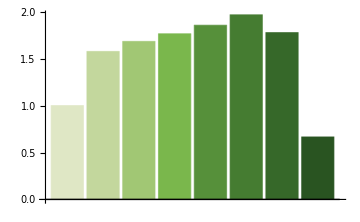
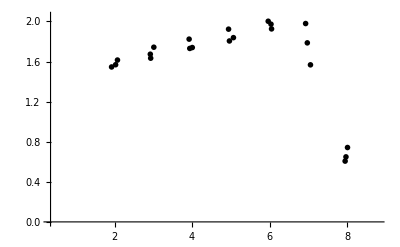
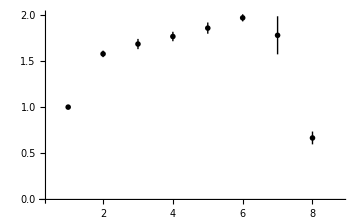

```mathematica
Overlay[{BarChart[{hmumetaboliteMean},ChartStyle->{RGBColor["#dfe7c5"],

RGBColor["#c3d79d"],

RGBColor["#a1c774"],

RGBColor["#7ab74c"],

RGBColor["#56903a"],
RGBColor["#457c31"],
RGBColor["#366829"],
RGBColor["#295421"]},AxesStyle->Directive[Black, 16],ImageSize->Medium],dots4,ListPlot[Map[Around[hmumetaboliteMean[[#]],hmumetaboliteerror[[#]]]&,Range[8]],PlotStyle->{Thick,Black},PlotRange->{{0.35,8.78},{0,2}},ImageSize->Medium,AxesStyle->Directive[Transparent, 16],PlotMarkers->{"", Tiny}]}]
```

```mathematica
{hyp300ckill1,hyp300ckill10,hyp300ckill50,hyp300ckill90,hyp300ckill99}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarhyp300c.mx"];
```

```mathematica
{hyp300ctyp1,hyp300ctyp10,hyp300ctyp50,hyp300ctyp90,hyp300ctyp99}=Parallelize[{titeryieldproductivity[hyp300ckill1],titeryieldproductivity[hyp300ckill10],titeryieldproductivity[hyp300ckill50],titeryieldproductivity[hyp300ckill90],titeryieldproductivity[hyp300ckill99]}];
```

```mathematica
{hyp400ckill1,hyp400ckill10,hyp400ckill50,hyp400ckill90,hyp400ckill99}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\errorbarhyp400c.mx"];
```

```mathematica
{hyp400ctyp1,hyp400ctyp10,hyp400ctyp50,hyp400ctyp90,hyp400ctyp99}=Parallelize[{titeryieldproductivity[hyp400ckill1],titeryieldproductivity[hyp400ckill10],titeryieldproductivity[hyp400ckill50],titeryieldproductivity[hyp400ckill90],titeryieldproductivity[hyp400ckill99]}];
```

```mathematica
{hypgen1,hypgen10,hypgen50,hypgen90,hypgen99,hypkeep1,hypkeep10,hypkeep50,hypkeep90,hypkeep99,hypmem1,hypmem10,hypmem50,hypmem90,hypmem99,hypkill1,hypkill10,hypkill50,hypkill90,hypkill99,hyptyp1,hyptyp10,hyptyp50,hyptyp90,hyptyp99}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\hyp500c24hpercent.mx"];
```

```mathematica
hypproteintyp300={ol300ctyp[[2]]/ol300ctyp[[2]],hyp300ctyp1[[2]]/ol300ctyp[[2]],hyp300ctyp10[[2]]/ol300ctyp[[2]],hyp300ctyp50[[2]]/ol300ctyp[[2]],hyp300ctyp90[[2]]/ol300ctyp[[2]],hyp300ctyp99[[2]]/ol300ctyp[[2]]};
```

```mathematica
hypproteintyp400={ol400ctyp[[2]]/ol400ctyp[[2]],hyp400ctyp1[[2]]/ol400ctyp[[2]],hyp400ctyp10[[2]]/ol400ctyp[[2]],hyp400ctyp50[[2]]/ol400ctyp[[2]],hyp400ctyp90[[2]]/ol400ctyp[[2]],hyp400ctyp99[[2]]/ol400ctyp[[2]]};
```

```mathematica
hypproteintyp500={oltyp[[2]]/oltyp[[2]],hyptyp1[[2]]/oltyp[[2]],hyptyp10[[2]]/oltyp[[2]],hyptyp50[[2]]/oltyp[[2]],hyptyp90[[2]]/oltyp[[2]],hyptyp99[[2]]/oltyp[[2]]};
```

```mathematica
hypproteinMean=Mean[{hypproteintyp300,hypproteintyp400,hypproteintyp500}]
```

{1.,1.55225,1.25596,0.996046,0.824612,0.661754}

```mathematica
hypproteinerror=StandardDeviation[{hypproteintyp300,hypproteintyp400,hypproteintyp500}]
```

{0.,0.0246806,0.0320729,0.0266385,0.0158765,0.0058417}

```mathematica
data5={hypproteintyp300,hypproteintyp400,hypproteintyp500};
```

```mathematica
rawPoints5=Flatten[Table[Transpose[{ConstantArray[xpos[[i]],Length[data5]],data5[[All,i]]}],{i,{2,3,4,5,6}}],1];
```

```mathematica
jittered5={#1+RandomReal[{-0.08,0.08}],#2}&@@@rawPoints5;

dots5=ListPlot[jittered5,PlotStyle->Black,PlotMarkers->{"OpenMarkers",5},AxesStyle->Directive[Transparent, 16],PlotRange->{{0.37,6.7},{0,1.62}}];
```

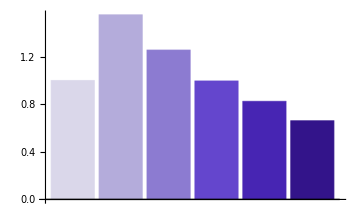
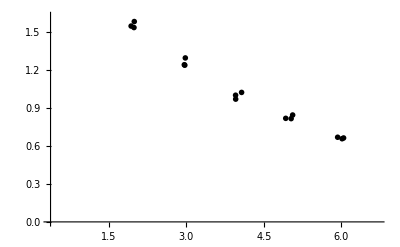
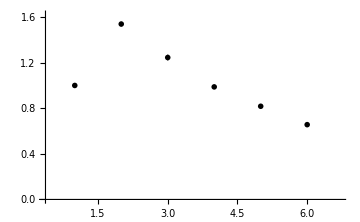

```mathematica
Overlay[{BarChart[{hypproteinMean},ChartStyle->{RGBColor["#dad7ea"],
RGBColor["#b4acdb"],
RGBColor["#8c7bd1"],
RGBColor["#6446cd"],
RGBColor["#4725b3"],
RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium],dots5,ListPlot[{Around[1,0],Around[1.5389,0.0191641],Around[1.2451,0.0248167],Around[0.98739,0.0184539],Around[0.817492,0.0107302],Around[0.656066,0.000739819]},PlotStyle->{Thick,Black},PlotRange->{{0.37,6.7},{0,1.62}},ImageSize->Medium,AxesStyle->Directive[Transparent, 16],PlotMarkers->{"", Tiny}]}]
```

```mathematica
hypmetabolitetyp300={ol300ctyp[[4]]/ol300ctyp[[4]],hyp300ctyp1[[4]]/ol300ctyp[[4]],hyp300ctyp10[[4]]/ol300ctyp[[4]],hyp300ctyp50[[4]]/ol300ctyp[[4]],hyp300ctyp90[[4]]/ol300ctyp[[4]],hyp300ctyp99[[4]]/ol300ctyp[[4]]};
```

```mathematica
hypmetabolitetyp400={ol400ctyp[[4]]/ol400ctyp[[4]],hyp400ctyp1[[4]]/ol400ctyp[[4]],hyp400ctyp10[[4]]/ol400ctyp[[4]],hyp400ctyp50[[4]]/ol400ctyp[[4]],hyp400ctyp90[[4]]/ol400ctyp[[4]],hyp400ctyp99[[4]]/ol400ctyp[[4]]};
```

```mathematica
hypmetabolitetyp500={oltyp[[4]]/oltyp[[4]],hyptyp1[[4]]/oltyp[[4]],hyptyp10[[4]]/oltyp[[4]],hyptyp50[[4]]/oltyp[[4]],hyptyp90[[4]]/oltyp[[4]],hyptyp99[[4]]/oltyp[[4]]};
```

```mathematica
hypmetaboliteMean=Mean[{hypmetabolitetyp300,hypmetabolitetyp400,hypmetabolitetyp500}]
```

{1.,1.02557,1.01613,1.01852,1.00474,0.999258}

```mathematica
hypmetaboliteerror=StandardDeviation[{hypmetabolitetyp300,hypmetabolitetyp400,hypmetabolitetyp500}]
```

{0.,0.0146998,0.0109701,0.0114056,0.00845467,0.0147234}

```mathematica
data6={hypmetabolitetyp300,hypmetabolitetyp400,hypmetabolitetyp500};
```

```mathematica
rawPoints6=Flatten[Table[Transpose[{ConstantArray[xpos[[i]],Length[data6]],data6[[All,i]]}],{i,{2,3,4,5,6}}],1];
```

```mathematica
jittered6={#1+RandomReal[{-0.08,0.08}],#2}&@@@rawPoints6;

dots6=ListPlot[jittered6,PlotStyle->Black,PlotMarkers->{"OpenMarkers",5},AxesStyle->Directive[Transparent, 16],PlotRange->{{0.37,6.7},{0,1.06}}];
```

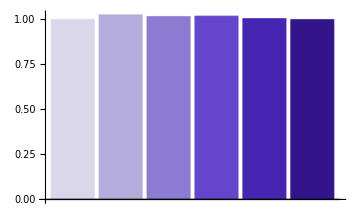
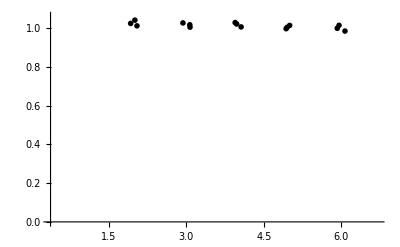
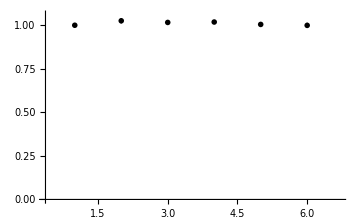

```mathematica
Overlay[{BarChart[{hypmetaboliteMean},ChartStyle->{RGBColor["#dad7ea"],
RGBColor["#b4acdb"],
RGBColor["#8c7bd1"],
RGBColor["#6446cd"],
RGBColor["#4725b3"],
RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium],dots6,ListPlot[Map[Around[hypmetaboliteMean[[#]],hypmetaboliteerror[[#]]]&,Range[6]],PlotStyle->{Thick,Black},PlotRange->{{0.37,6.7},{0,1.06}},ImageSize->Medium,AxesStyle->Directive[Transparent, 16],PlotMarkers->{"", Tiny}]}]
```

```mathematica
{hmp300ctyp1,hmp300ctyp10,hmp300ctyp50,hmp300ctyp90,hmp300ctyp99}=Parallelize[{titeryieldproductivity[hmp300ckill1],titeryieldproductivity[hmp300ckill10],titeryieldproductivity[hmp300ckill50],titeryieldproductivity[hmp300ckill90],titeryieldproductivity[hmp300ckill99]}];
```

```mathematica
{hmp400ctyp1,hmp400ctyp10,hmp400ctyp50,hmp400ctyp90,hmp400ctyp99}=Parallelize[{titeryieldproductivity[hmp400ckill1],titeryieldproductivity[hmp400ckill10],titeryieldproductivity[hmp400ckill50],titeryieldproductivity[hmp400ckill90],titeryieldproductivity[hmp400ckill99]}];
```

```mathematica
{hmpgen1,hmpgen10,hmpgen50,hmpgen90,hmpgen99,hmpkeep1,hmpkeep10,hmpkeep50,hmpkeep90,hmpkeep99,hmpmem1,hmpmem10,hmpmem50,hmpmem90,hmpmem99,hmpkill1,hmpkill10,hmpkill50,hmpkill90,hmpkill99,hmptyp1,hmptyp10,hmptyp50,hmptyp90,hmptyp99}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\hmp500c24hpercent.mx"];
```

```mathematica
hmpproteintyp300={ol300ctyp[[2]]/ol300ctyp[[2]],hmp300ctyp1[[2]]/ol300ctyp[[2]],hmp300ctyp10[[2]]/ol300ctyp[[2]],hmp300ctyp50[[2]]/ol300ctyp[[2]],hmp300ctyp90[[2]]/ol300ctyp[[2]],hmp300ctyp99[[2]]/ol300ctyp[[2]]};
```

```mathematica
hmpproteintyp400={ol400ctyp[[2]]/ol400ctyp[[2]],hmp400ctyp1[[2]]/ol400ctyp[[2]],hmp400ctyp10[[2]]/ol400ctyp[[2]],hmp400ctyp50[[2]]/ol400ctyp[[2]],hmp400ctyp90[[2]]/ol400ctyp[[2]],hmp400ctyp99[[2]]/ol400ctyp[[2]]};
```

```mathematica
hmpproteintyp500={oltyp[[2]]/oltyp[[2]],hmptyp1[[2]]/oltyp[[2]],hmptyp10[[2]]/oltyp[[2]],hmptyp50[[2]]/oltyp[[2]],hmptyp90[[2]]/oltyp[[2]],hmptyp99[[2]]/oltyp[[2]]};
```

```mathematica
hmpproteinMean=Mean[{hmpproteintyp300,hmpproteintyp400,hmpproteintyp500}]
```

{1.,1.16007,1.03895,1.0002,0.949747,0.846565}

```mathematica
hmpproteinerror=StandardDeviation[{hmpproteintyp300,hmpproteintyp400,hmpproteintyp500}]
```

{0.,0.0113744,0.0206606,0.0265906,0.0128093,0.0101725}

```mathematica
data7={hmpproteintyp300,hmpproteintyp400,hmpproteintyp500};
```

```mathematica
rawPoints7=Flatten[Table[Transpose[{ConstantArray[xpos[[i]],Length[data7]],data7[[All,i]]}],{i,{2,3,4,5,6}}],1];
```

```mathematica
jittered7={#1+RandomReal[{-0.08,0.08}],#2}&@@@rawPoints7;

dots7=ListPlot[jittered7,PlotStyle->Black,PlotMarkers->{"OpenMarkers",5},AxesStyle->Directive[Transparent, 16],PlotRange->{{0.37,6.7},{0,1.2}}];
```

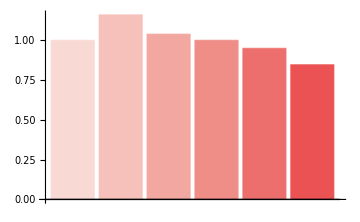
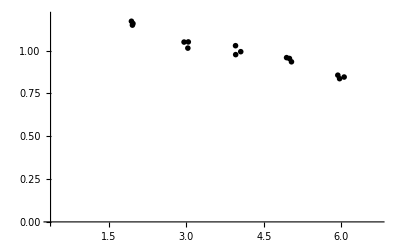
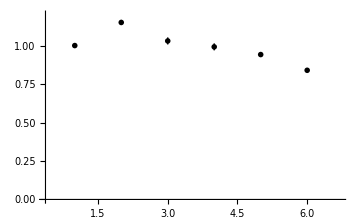

```mathematica
Overlay[{BarChart[{hmpproteinMean},ChartStyle->{RGBColor["#f8d9d3"],
RGBColor["#f5c1ba"],
RGBColor["#f2a8a1"],
RGBColor["#ef8d87"],
RGBColor["#ed6f6d"],
RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium],dots7, ListPlot[{Around[1,0],Around[1.15017,0.0165624],Around[1.03008,0.0229431],Around[0.991569,0.0227478],Around[0.941562,0.0055016],Around[0.839348,0.0139819]},PlotStyle->{Thick,Black},PlotRange->{{0.37,6.7},{0,1.2}},ImageSize->Medium,AxesStyle->Directive[Transparent, 16],PlotMarkers->{"", Tiny}]}]
```

```mathematica
hmpmetabolitetyp300={ol300ctyp[[4]]/ol300ctyp[[4]],hmp300ctyp1[[4]]/ol300ctyp[[4]],hmp300ctyp10[[4]]/ol300ctyp[[4]],hmp300ctyp50[[4]]/ol300ctyp[[4]],hmp300ctyp90[[4]]/ol300ctyp[[4]],hmp300ctyp99[[4]]/ol300ctyp[[4]]};
```

```mathematica
hmpmetabolitetyp400={ol400ctyp[[4]]/ol400ctyp[[4]],hmp400ctyp1[[4]]/ol400ctyp[[4]],hmp400ctyp10[[4]]/ol400ctyp[[4]],hmp400ctyp50[[4]]/ol400ctyp[[4]],hmp400ctyp90[[4]]/ol400ctyp[[4]],hmp400ctyp99[[4]]/ol400ctyp[[4]]};
```

```mathematica
hmpmetabolitetyp500={oltyp[[4]]/oltyp[[4]],hmptyp1[[4]]/oltyp[[4]],hmptyp10[[4]]/oltyp[[4]],hmptyp50[[4]]/oltyp[[4]],hmptyp90[[4]]/oltyp[[4]],hmptyp99[[4]]/oltyp[[4]]};
```

```mathematica
hmpmetaboliteMean=Mean[{hmpmetabolitetyp300,hmpmetabolitetyp400,hmpmetabolitetyp500}]
```

{1.,1.01829,0.988999,1.01511,1.01851,1.00392}

```mathematica
hmpmetaboliteerror=StandardDeviation[{hmpmetabolitetyp300,hmpmetabolitetyp400,hmpmetabolitetyp500}]
```

{0.,0.0135036,0.0290626,0.0253189,0.0173933,0.00968555}

```mathematica
data8={hmpmetabolitetyp300,hmpmetabolitetyp400,hmpmetabolitetyp500};
```

```mathematica
rawPoints8=Flatten[Table[Transpose[{ConstantArray[xpos[[i]],Length[data8]],data8[[All,i]]}],{i,{2,3,4,5,6}}],1];
```

```mathematica
jittered8={#1+RandomReal[{-0.08,0.08}],#2}&@@@rawPoints8;

dots8=ListPlot[jittered8,PlotStyle->Black,PlotMarkers->{"OpenMarkers",5},AxesStyle->Directive[Transparent, 16],PlotRange->{{0.37,6.7},{0,1.07}}];
```

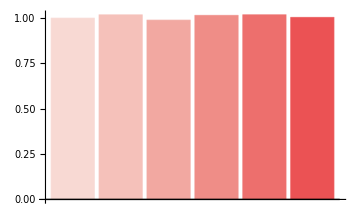
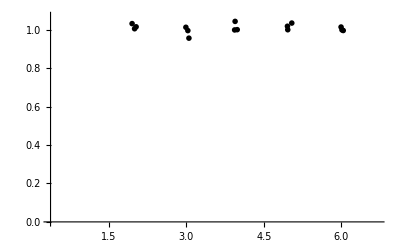
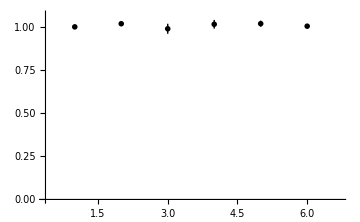

```mathematica
Overlay[{BarChart[{hmpmetaboliteMean},ChartStyle->{RGBColor["#f8d9d3"],
RGBColor["#f5c1ba"],
RGBColor["#f2a8a1"],
RGBColor["#ef8d87"],
RGBColor["#ed6f6d"],
RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium],dots8,ListPlot[Map[Around[hmpmetaboliteMean[[#]],hmpmetaboliteerror[[#]]]&,Range[6]],PlotStyle->{Thick,Black},PlotRange->{{0.37,6.7},{0,1.07}},ImageSize->Medium,AxesStyle->Directive[Transparent, 16],PlotMarkers->{"", Tiny}]}]
```